## Governing ODE and BCs for static landslide on non-planar base

The above ODE describes static equilibrium for a landslide with frictional boundary conditions

```mathematica
θv = π/5;
fv =1.2*Tan[θv];
bmax = 0.15;
bv = bmax*Sin[ 1π x];
(*bv =4 bmax*(x^2+x);(* quadratic basal topography*)*)
eqnODE = -D[H[x],x] - 0.5*(Tan[θv]-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*Tan[θv])*H[x] == fv+D[bv,x] -(Tan[θv]-D[bv,x])/(1+D[bv,x]*Tan[θv])
solss = NDSolve[{eqnODE,H[-0]==0.0},H,{x,-1,0}];
(*h = bv+ H[x]/. solss;*)
```

(0.74022 (√(5-2 √5)-0.471239 Cos[π x]) H[x] Sin[π x])/((1+0.342375 Cos[π x]) (1+0.222066 Cos[π x]^2))-H'[x]==0.871851-(√(5-2 √5)-0.471239 Cos[π x])/(1+0.342375 Cos[π x])+0.471239 Cos[π x]

## Instead of simply integrating , let us log-transform to such that the solution is strictly positive

```mathematica
eqnlogODE = -Exp[ϕ[x]]*D[ϕ[x],x] - 0.5*(Tan[θv]-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*Tan[θv])*Exp[ϕ[x]] == fv+D[bv,x] -(Tan[θv]-D[bv,x])/(1+D[bv,x]*Tan[θv]);
sollogss = NDSolve[{eqnlogODE,ϕ[0]==-100},ϕ,{x,-1,0}];
H2 =  Exp[ϕ[x]/.sollogss];
h = bv+ H2;
```

## Plot results

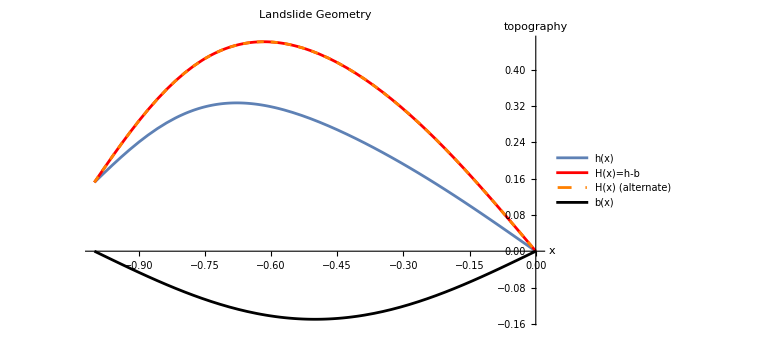

```mathematica
p1=Plot[{h,H2,H[x]/. solss,bv},{x,-1,0},PlotStyle->{DarkBlue,{Red,Thick},{Orange,Dashed},Black},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","H(x)=h-b","H(x) (alternate)","b(x)"},ImageSize->Large,PlotRange->Full]
```

## Incorporate ice barrier to landslide geometry

{-(0.0871851 (0.151721+√(5-2 √5) x-H[x]+0.15 Sin[3.14159 x]))/H[x]-(0.74022 (√(5-2 √5)+0.471239 Cos[3.14159 x]) H[x] Sin[3.14159 x])/((1-0.342375 Cos[3.14159 x]) (1+0.222066 Cos[3.14159 x]^2))-0.148044 ((√(5-2 √5))/(1-0.342375 Cos[3.14159 x])+(0.471239 Cos[3.14159 x])/(1+0.222066 Cos[3.14159 x]^2)) (0.151721+√(5-2 √5) x-H[x]+0.15 Sin[3.14159 x]) Sin[3.14159 x]-0.9 (-0.471239 Cos[3.14159 x]+H'[x])}==0.944505-(√(5-2 √5)+0.471239 Cos[3.14159 x])/(1-0.342375 Cos[3.14159 x])

NDSolve::ndsz: At x == 0.820778, step size is effectively zero; singularity or stiff system suspected.

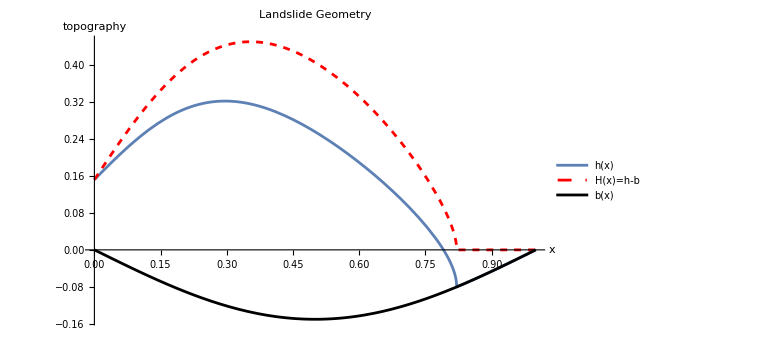

```mathematica
(*bv = b[x];*)
hg = (H2/.x->-1);
θi = θv;
bv = -bmax*Sin[ 1.0π x];
ρ = 0.1;
eqiceODE = (ρ-1)(D[H[x],x]+D[bv,x]) - ((Tan[θv]-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*Tan[θv]))*H[x]/2 - ρ*(hg - H[x]-bv + x*Tan[θi])fv/H[x] -ρ*(hg - H[x]-bv + x*Tan[θi])*D[bv,x,x]*(Tan[θv]/(1+D[bv,x]*Tan[θv])-D[bv,x]/ (1+(D[bv,x])^2))==fv + ρ Tan[θv]-(Tan[θv]-D[bv,x])/(1+D[bv,x]*Tan[θv])
solice = NDSolve[{eqiceODE,H[0]==hg},H,{x,0,1}];
Hice=Min[Max[0,H[x]/.solice],1];
hice = bv+ Hice;
p2=Plot[{hice,Hice,bv},{x,0,1},PlotStyle->{DarkBlue,{Red,Dashed},Black},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","H(x)=h-b","b(x)"},ImageSize->Large,PlotRange->Full]
```